```mathematica
dataAll = Import["~//Documents/PhD-quali/zeca-analise/join_count_acertos.csv"];
```

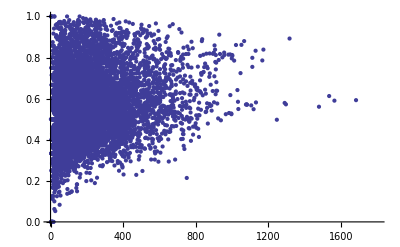

```mathematica
ListPlot[dataAll[[All,{2,5}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

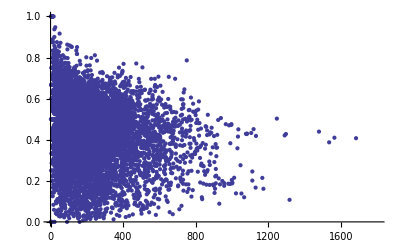

```mathematica
ListPlot[dataAll[[All,{2,6}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

```mathematica
IndependenceTest[dataAll[[All,2]], dataAll[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.161357 | 2.30134×10^-46
Goodman-Kruskal γ | 0.16618 | 2.60324×10^-109
Hoeffding 𝒟 | 0.0176173 | 0.
Kendall τ | 0.165889 | 2.5904×10^-109
Spearman Rank | 0.24564 | 2.96093×10^-110, | Statistic
Spearman Rank | 0.24564}

```mathematica
Correlation[dataAll,2]],data[[All,5]]]
```

0.208672

```mathematica
dataH = Import["~/Documents/PhD-quali/zeca-analise/join_count_acertos_h.csv"];
```

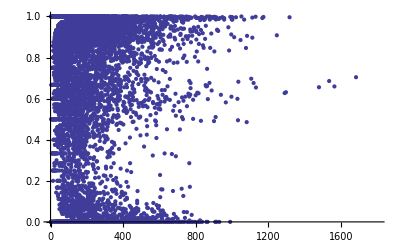

```mathematica
ListPlot[dataH[[All,{2,5}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

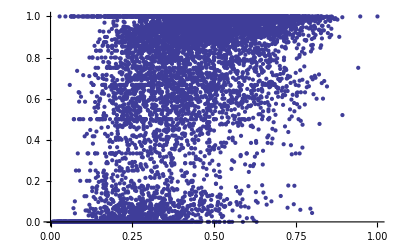

```mathematica
ListPlot[dataH[[All,{7,5}]], PlotRange->{{0,1},{0,1}}, PlotTheme->"Classic"]
```

```mathematica
ListPointPlot3D[dataH[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataH[[All,{8,7,5}]], PlotRange->{{0,1300},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

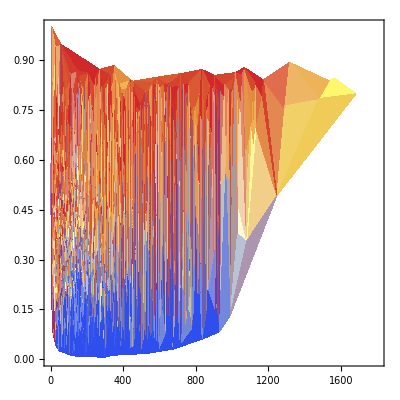

```mathematica
ListDensityPlot[dataH[[All,{2,7,5}]],InterpolationOrder->1, PlotRange->{{0,1800},{0,1},{0,1}},ColorFunction->"Temperature"]
```

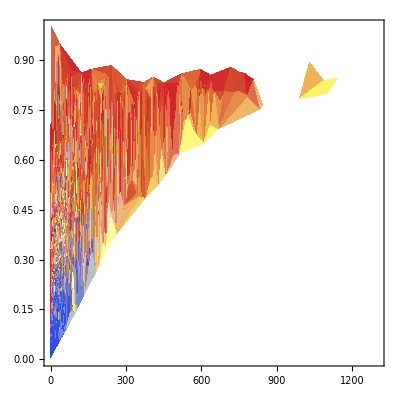

```mathematica
ListDensityPlot[dataH[[All,{8,7,5}]],InterpolationOrder->1, PlotRange->{{0,1300},{0,1},{0,1}},ColorFunction->"Temperature"]
```

```mathematica
IndependenceTest[dataH[[All,2]], dataH[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | -0.0453353 | 0.0000369287
Goodman-Kruskal γ | -0.0886737 | 5.29978×10^-29
Hoeffding 𝒟 | 0.00605923 | 0.
Kendall τ | -0.0860739 | 2.93025×10^-29
Spearman Rank | -0.128785 | 8.79833×10^-31, | Statistic
Spearman Rank | -0.128785}

```mathematica
Correlation[dataH[[All,2]],dataH[[All,5]]]
```

-0.0455421

```mathematica
IndependenceTest[dataH[[All,7]], dataH[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.438251 | 2.89045295280919×10^-342
Goodman-Kruskal γ | 0.446092 | 5.39646586847266×10^-691
Hoeffding 𝒟 | 0.133843 | 0.
Kendall τ | 0.433313 | 1.78439334721135×10^-697
Spearman Rank | 0.597464 | 2.1770108553×10^-765, | Statistic
Spearman Rank | 0.597464}

```mathematica
Correlation[dataH[[All,7]],dataH[[All,5]]]
```

0.614328

```mathematica
IndependenceTest[dataH[[All,8]], dataH[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.18668 | 6.27818×10^-59
Goodman-Kruskal γ | 0.179608 | 5.05787×10^-112
Hoeffding 𝒟 | 0.025858 | 0.
Kendall τ | 0.173844 | 4.50493×10^-113
Spearman Rank | 0.235369 | 1.31294×10^-100, | Statistic
Spearman Rank | 0.235369}

```mathematica
Correlation[dataH[[All,8]],dataH[[All,5]]]
```

0.257814

```mathematica
dataE = Import["Documents/PhD-quali/zeca-analise/join_count_acertos_e.csv"];
```

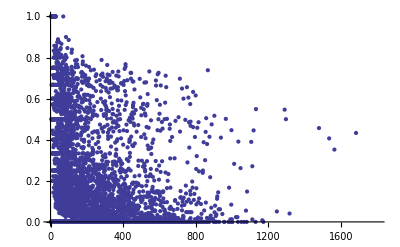

```mathematica
ListPlot[dataE[[All,{2,5}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

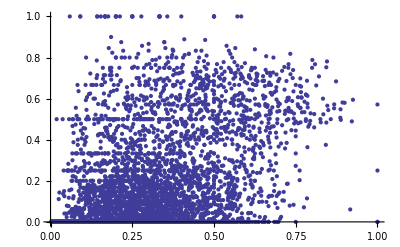

```mathematica
ListPlot[dataE[[All,{7,5}]], PlotRange->{{0,1},{0,1}}, PlotTheme->"Classic"]
```

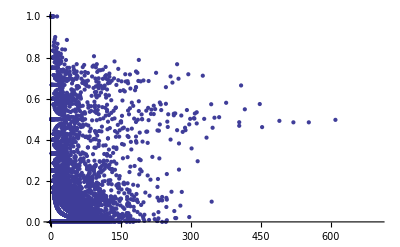

```mathematica
ListPlot[dataE[[All,{8,5}]], PlotRange->{{0,700},{0,1}}, PlotTheme->"Classic"]
```

```mathematica
ListPointPlot3D[dataE[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataE[[All,{8,7,5}]], PlotRange->{{0,800},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

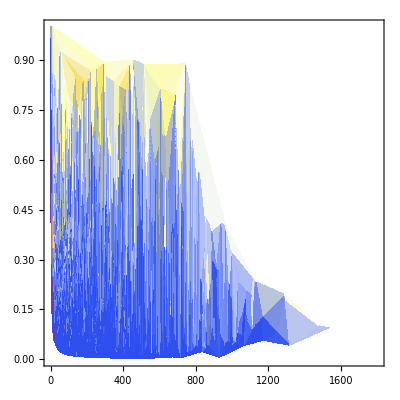

```mathematica
ListDensityPlot[dataE[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

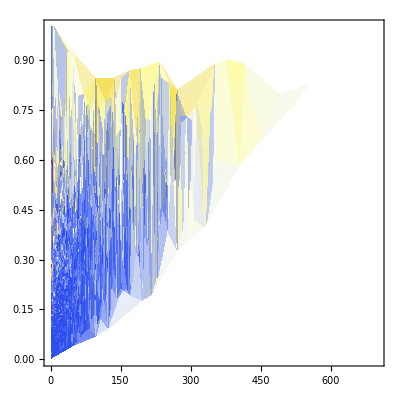

```mathematica
ListDensityPlot[dataE[[All,{8,7,5}]], PlotRange->{{0,700},{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

```mathematica
IndependenceTest[dataE[[All,2]], dataE[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | -0.0260439 | 8.88178×10^-16
Goodman-Kruskal γ | -0.0782437 | 1.53073×10^-10
Hoeffding 𝒟 | 0.00409482 | 0.
Kendall τ | -0.0615072 | 2.55086×10^-13
Spearman Rank | -0.085497 | 3.9669×10^-14, | Statistic
Spearman Rank | -0.085497}

```mathematica
Correlation[dataE[[All,2]],dataE[[All,5]]]
```

-0.0939965

```mathematica
IndependenceTest[dataE[[All,7]], dataE[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.515807 | 7.03944×10^-18
Goodman-Kruskal γ | 0.581928 | 2.51880825082023×10^-496
Hoeffding 𝒟 | 0.0852364 | 0.
Kendall τ | 0.457817 | 1.98605973101508×10^-647
Spearman Rank | 0.600026 | 4.8169120472×10^-758, | Statistic
Spearman Rank | 0.600026}

```mathematica
Correlation[dataE[[All,7]],dataE[[All,5]]]
```

0.531294

```mathematica
IndependenceTest[dataE[[All,8]], dataE[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.35688 | 0.1602
Goodman-Kruskal γ | 0.368573 | 1.80712×10^-195
Hoeffding 𝒟 | 0.0309891 | 0.
Kendall τ | 0.289226 | 8.9089×10^-255
Spearman Rank | 0.385913 | 2.58065×10^-275, | Statistic
Spearman Rank | 0.385913}

```mathematica
Correlation[dataE[[All,8]],dataE[[All,5]]]
```

0.255789

```mathematica
dataC = Import["~/Documents/PhD-quali/zeca-analise/join_count_acertos_c.csv"];
```

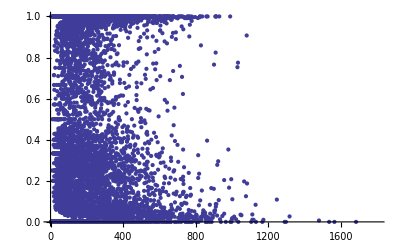

```mathematica
ListPlot[dataC[[All,{2,5}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

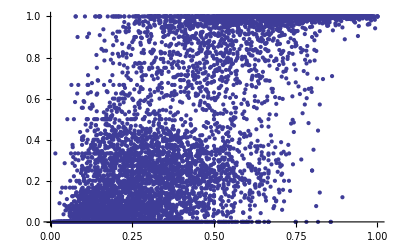

```mathematica
ListPlot[dataC[[All,{7,5}]], PlotRange->{{0,1},{0,1}}, PlotTheme->"Classic"]
```

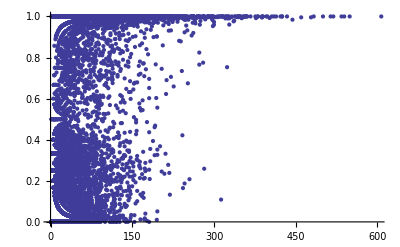

```mathematica
ListPlot[dataC[[All,{8,5}]], PlotRange->{{0,600},{0,1}}, PlotTheme->"Classic"]
```

```mathematica
ListPointPlot3D[dataC[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataC[[All,{8,7,5}]], PlotRange->{{0,600},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

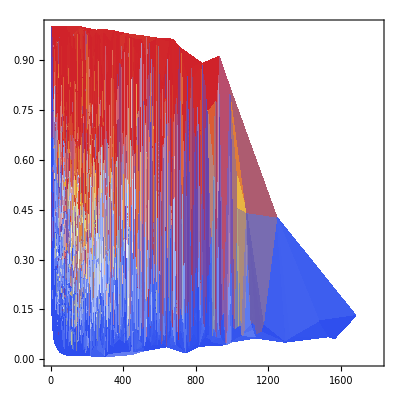

```mathematica
ListDensityPlot[dataC[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

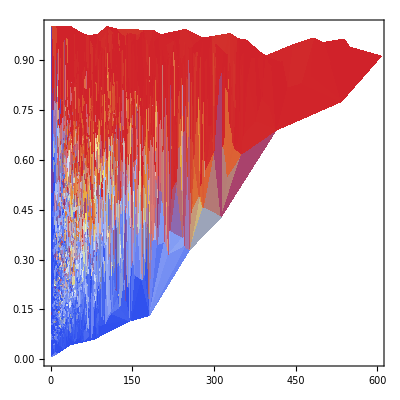

```mathematica
ListDensityPlot[dataC[[All,{8,7,5}]], PlotRange->{{0,600},{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

```mathematica
IndependenceTest[dataC[[All,2]], dataC[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.127619 | 1.41335×10^-29
Goodman-Kruskal γ | 0.147421 | 9.36809×10^-72
Hoeffding 𝒟 | 0.0148022 | 0.
Kendall τ | 0.14051 | 3.99513×10^-73
Spearman Rank | 0.208569 | 6.36021×10^-79, | Statistic
Spearman Rank | 0.208569}

```mathematica
Correlation[dataC[[All,2]],dataC[[All,5]]]
```

0.0641282

```mathematica
IndependenceTest[dataC[[All,7]], dataC[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.558721 | 2.30877475586412×10^-562
Goodman-Kruskal γ | 0.600064 | 6.81055817907162×10^-1161
Hoeffding 𝒟 | 0.231257 | 0.
Kendall τ | 0.572405 | 1.34903814418885×10^-1183
Spearman Rank | 0.753156 | 1.7162502351×10^-1449, | Statistic
Spearman Rank | 0.753156}

```mathematica
Correlation[dataC[[All,7]],dataC[[All,5]]]
```

0.776096

```mathematica
IndependenceTest[dataC[[All,8]], dataC[[All,5]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.402862 | 1.75603×10^-281
Goodman-Kruskal γ | 0.459543 | 8.6086772182691×10^-672
Hoeffding 𝒟 | 0.114894 | 0.
Kendall τ | 0.43714 | 5.19180207640555×10^-685
Spearman Rank | 0.599583 | 4.0093736155×10^-772, | Statistic
Spearman Rank | 0.599583}

```mathematica
Correlation[dataC[[All,8]],dataC[[All,5]]]
```

0.51075